# Physics through Computational Thinking Week-5: Dynamics Through Numerical Methods

In this tutorial, we use Mathematica for solving and visualizing dynamical systems. We discuss the numerical techniques for solving ordinary differential equations (ODEs). Many systems in nature, for example: the cooling of a cup of coffee and the motion of a double pendulum, do not have simple analytical solutions.

## 1. Euler’s Method (Linear Approximation)

The core idea of numerical methods for an ODE, dy/dt=f(y,t) -- is to approximate the next value y_(n+1) using the current value y_n and a small time step .

Linear approximation:  y_(n+1)=y_n+h f(t_n,y_n)  , t_(n+1)=t_n+h . (slope is constant)

Application: Newton’s Law of Cooling

The rate of change of the temperature T of an object is

dT/dt=-k (T-T_env) ,

where k>0, and T_env is the ambient temperature.

Exact Solution --  T(t)=T_env+(T_0-T_env)e^-kt .

Now, we test this via numerical methods.

```mathematica
k=0.3;
Tenv=25;
T0=90;
```

```mathematica
f[t_,T_]:=-k (T-Tenv);
```

```mathematica
EulerMethod[f_,y0_,{t0_,tmax_},h_]:=
Module[{tlist,ylist,nsteps},
tlist=Range[t0,tmax,h];
nsteps=Length[tlist];
ylist=ConstantArray[0,nsteps];
ylist[[1]]=y0;

Do[
ylist[[n+1]]=ylist[[n]]+h f[tlist[[n]],ylist[[n]]],
{n,1,nsteps-1}
];
Transpose[{tlist,ylist}]
]
```

```mathematica
tlist={0,0.1,0.2,0.3};
ylist={1,0.82,0.67,0.55};
```

```mathematica
{tlist,ylist}
```

{{0,0.1,0.2,0.3},{1,0.82,0.67,0.55}}

```mathematica
Transpose[{tlist,ylist}]
```

{{0,1},{0.1,0.82},{0.2,0.67},{0.3,0.55}}

```mathematica
solEuler=EulerMethod[f,T0,{0,20},0.5]
```

{{0.,90},{0.5,80.25},{1.,71.9625},{1.5,64.9181},{2.,58.9304},{2.5,53.8408},{3.,49.5147},{3.5,45.8375},{4.,42.7119},{4.5,40.0551},{5.,37.7968},{5.5,35.8773},{6.,34.2457},{6.5,32.8589},{7.,31.68},{7.5,30.678},{8.,29.8263},{8.5,29.1024},{9.,28.487},{9.5,27.964},{10.,27.5194},{10.5,27.1415},{11.,26.8202},{11.5,26.5472},{12.,26.3151},{12.5,26.1179},{13.,25.9502},{13.5,25.8077},{14.,25.6865},{14.5,25.5835},{15.,25.496},{15.5,25.4216},{16.,25.3584},{16.5,25.3046},{17.,25.2589},{17.5,25.2201},{18.,25.1871},{18.5,25.159},{19.,25.1352},{19.5,25.1149},{20.,25.0976}}

```mathematica
Texact[t_]:=Tenv+(T0-Tenv) Exp[-k t];
```

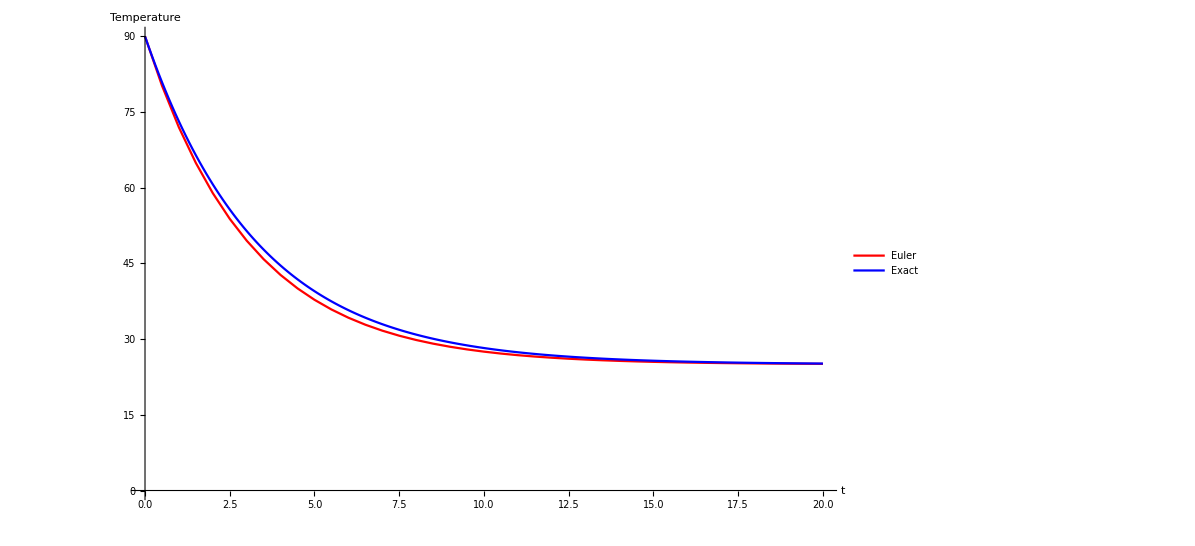

```mathematica
ListLinePlot[{solEuler,Table[{t,Texact[t]},{t,0,20,0.1}]},PlotLegends->{"Euler","Exact"},PlotStyle->{Red,Blue},AxesLabel->{"t","Temperature"}]
```

```mathematica
Mean[Abs[solEuler[[All,2]]-Texact/@solEuler[[All,1]]]] (*Mean Global Error*)
```

0.801706

The operator /@ means Map.

{1.60872,0.801706,0.31992,0.159823}

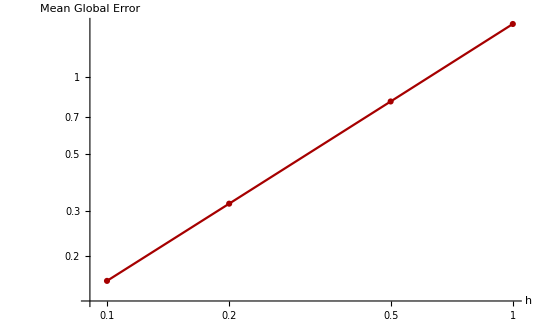

```mathematica
hvalues={1,0.5,0.2,0.1};

errors=Table[sol=EulerMethod[f,T0,{0,20},h];
Mean[Abs[sol[[All,2]]-Texact/@sol[[All,1]]]],{h,hvalues}]

ListLogLogPlot[Transpose[{hvalues,errors}],Joined->True,PlotMarkers->Automatic,AxesLabel->{"h","Mean Global Error"}]
```

## 2. Runge-Kutta 2 (RK2 / Midpoint Method)

Euler method is often inaccurate because it only uses the slope at the beginning of the interval. RK2/Midpoint method improves on this by taking a "trial step" at the midpoint, calculating the slope there, and taking the entire step using that slope.

k_1=f(t_n,y_n) ,    t_(n+1)=t_n+h ,
y_(n+1)=y_n+h f(t_n+h/2,y_n+h/2 k_1) .

This gives second-order accuracy:
Local error: O(h^3)
Global error: O(h^2)

```mathematica
RK2[f_,y0_,{t0_,tmax_},h_]:=
Module[{tlist,ylist,nsteps,k1},
tlist=Range[t0,tmax,h];
nsteps=Length[tlist];
ylist=ConstantArray[0,nsteps];
ylist[[1]]=y0;

Do[
k1=f[tlist[[n]],ylist[[n]]];
ylist[[n+1]]=ylist[[n]]+h f[tlist[[n]]+(h/2),ylist[[n]]+(h/2) k1];,
{n,1,nsteps-1}
];
Transpose[{tlist,ylist}]
]
```

```mathematica
solRK2=RK2[f,T0,{0,20},0.5]
```

{{0.,90},{0.5,80.9813},{1.,73.2139},{1.5,66.5242},{2.,60.7627},{2.5,55.8006},{3.,51.527},{3.5,47.8464},{4.,44.6765},{4.5,41.9464},{5.,39.5951},{5.5,37.57},{6.,35.8259},{6.5,34.3238},{7.,33.0301},{7.5,31.916},{8.,30.9564},{8.5,30.1299},{9.,29.4181},{9.5,28.8051},{10.,28.2772},{10.5,27.8225},{11.,27.4308},{11.5,27.0936},{12.,26.8031},{12.5,26.5529},{13.,26.3374},{13.5,26.1519},{14.,25.992},{14.5,25.8544},{15.,25.7359},{15.5,25.6338},{16.,25.5458},{16.5,25.4701},{17.,25.4049},{17.5,25.3487},{18.,25.3003},{18.5,25.2586},{19.,25.2228},{19.5,25.1918},{20.,25.1652}}

```mathematica
solEuler=EulerMethod[f,T0,{0,20},0.5]
```

{{0.,90},{0.5,80.25},{1.,71.9625},{1.5,64.9181},{2.,58.9304},{2.5,53.8408},{3.,49.5147},{3.5,45.8375},{4.,42.7119},{4.5,40.0551},{5.,37.7968},{5.5,35.8773},{6.,34.2457},{6.5,32.8589},{7.,31.68},{7.5,30.678},{8.,29.8263},{8.5,29.1024},{9.,28.487},{9.5,27.964},{10.,27.5194},{10.5,27.1415},{11.,26.8202},{11.5,26.5472},{12.,26.3151},{12.5,26.1179},{13.,25.9502},{13.5,25.8077},{14.,25.6865},{14.5,25.5835},{15.,25.496},{15.5,25.4216},{16.,25.3584},{16.5,25.3046},{17.,25.2589},{17.5,25.2201},{18.,25.1871},{18.5,25.159},{19.,25.1352},{19.5,25.1149},{20.,25.0976}}

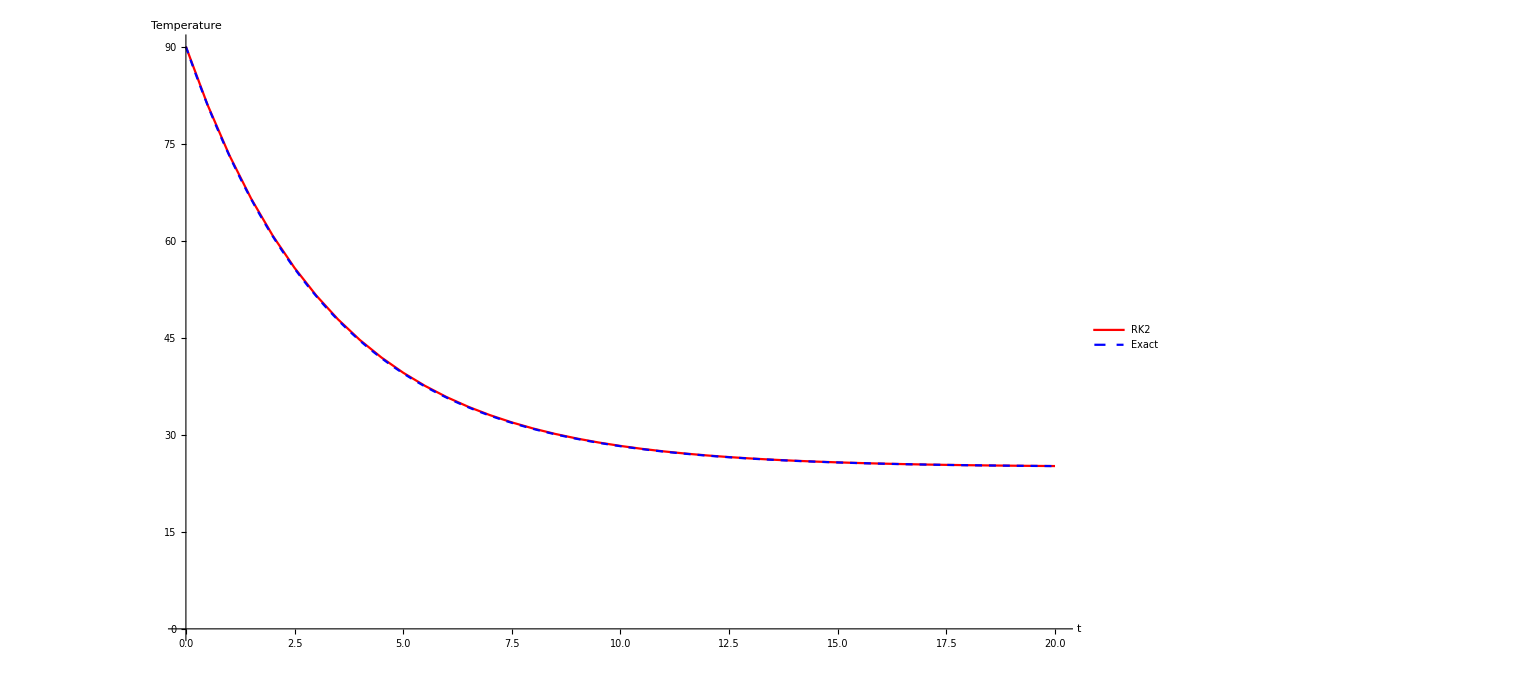

```mathematica
ListLinePlot[{solRK2,Table[{t,Texact[t]},{t,0,20,0.1}]},PlotLegends->{"RK2","Exact"},PlotStyle->{{Red},{Blue,Dashed}},AxesLabel->{"t","Temperature"}]
```

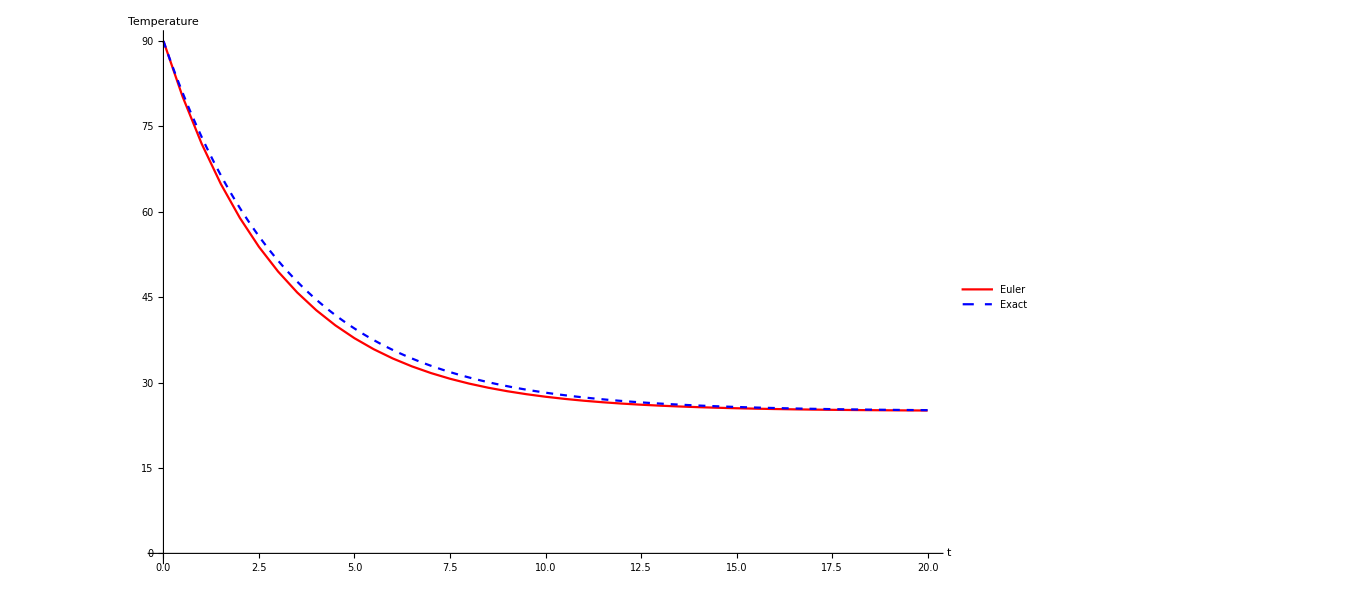

```mathematica
ListLinePlot[{solEuler,Table[{t,Texact[t]},{t,0,20,0.1}]},PlotLegends->{"Euler","Exact"},PlotStyle->{{Red},{Blue,Dashed}},AxesLabel->{"t","Temperature"}]
```

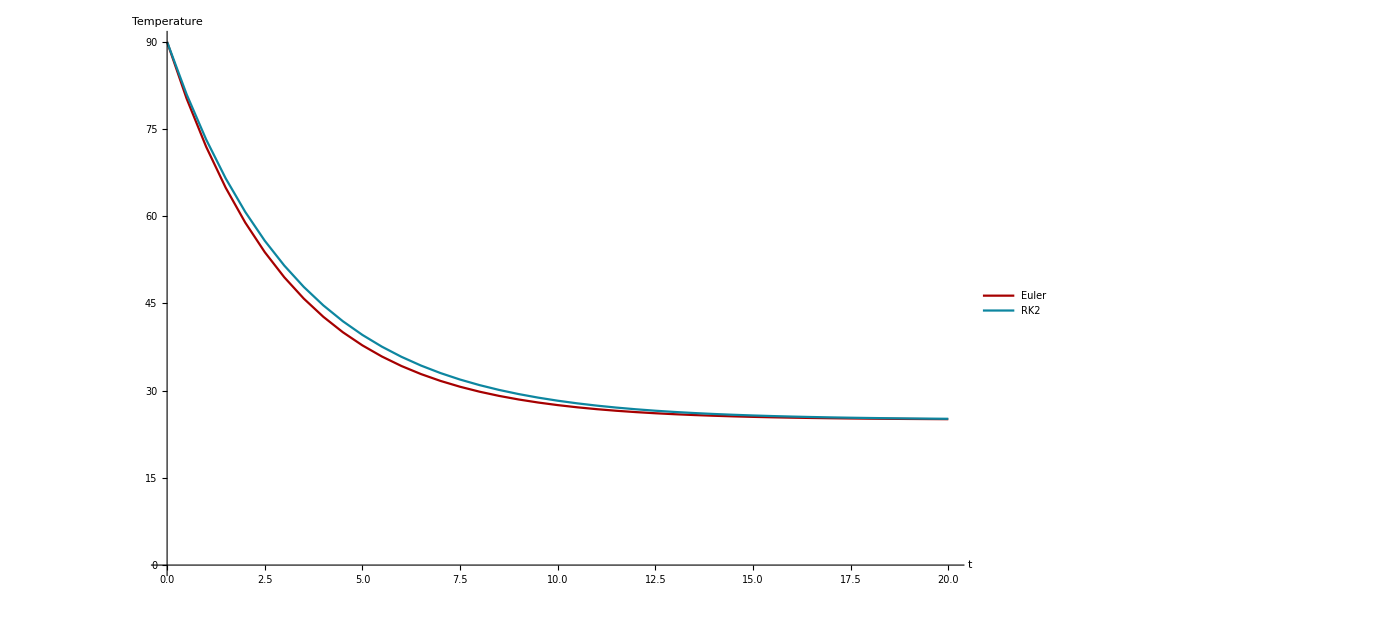

```mathematica
solEuler=EulerMethod[f,T0,{0,20},0.5];

ListLinePlot[{solEuler,solRK2},PlotLegends->{"Euler","RK2","Exact"},AxesLabel->{"t","Temperature"}]
```

Results: Euler deviates more, while RK2 is almost overlap (or significantly closer) .

```mathematica
Mean[Abs[solRK2[[All,2]]-Texact/@solRK2[[All,1]]]]  (*Mean Global Error*)
```

0.0437297

Compare with Euler error,

```mathematica
Mean[Abs[solEuler[[All,2]]-Texact/@solEuler[[All,1]]]] (*Mean Global Error*)
```

0.801706

Global error in RK2 ~ O(h^2) , while the Global error in Euler ~ O(h) .

Example: A vertically falling object with quadratic drag force.

d/dt v= g - c/m v|v|

where c is the drag coefficient. At t=0, v=0.

```mathematica
g=9.8;
m=1;
c=1.2;

f[t_,v_]:=g-(c/m) v Abs[v];
```

```mathematica
vexact=NDSolve[{v'[t]==g-(c/m) v[t] Abs[v[t]],v[0]==0},v,{t,0,10}];
```

```mathematica
solRK2=RK2[f,0,{0,10},0.2];
```

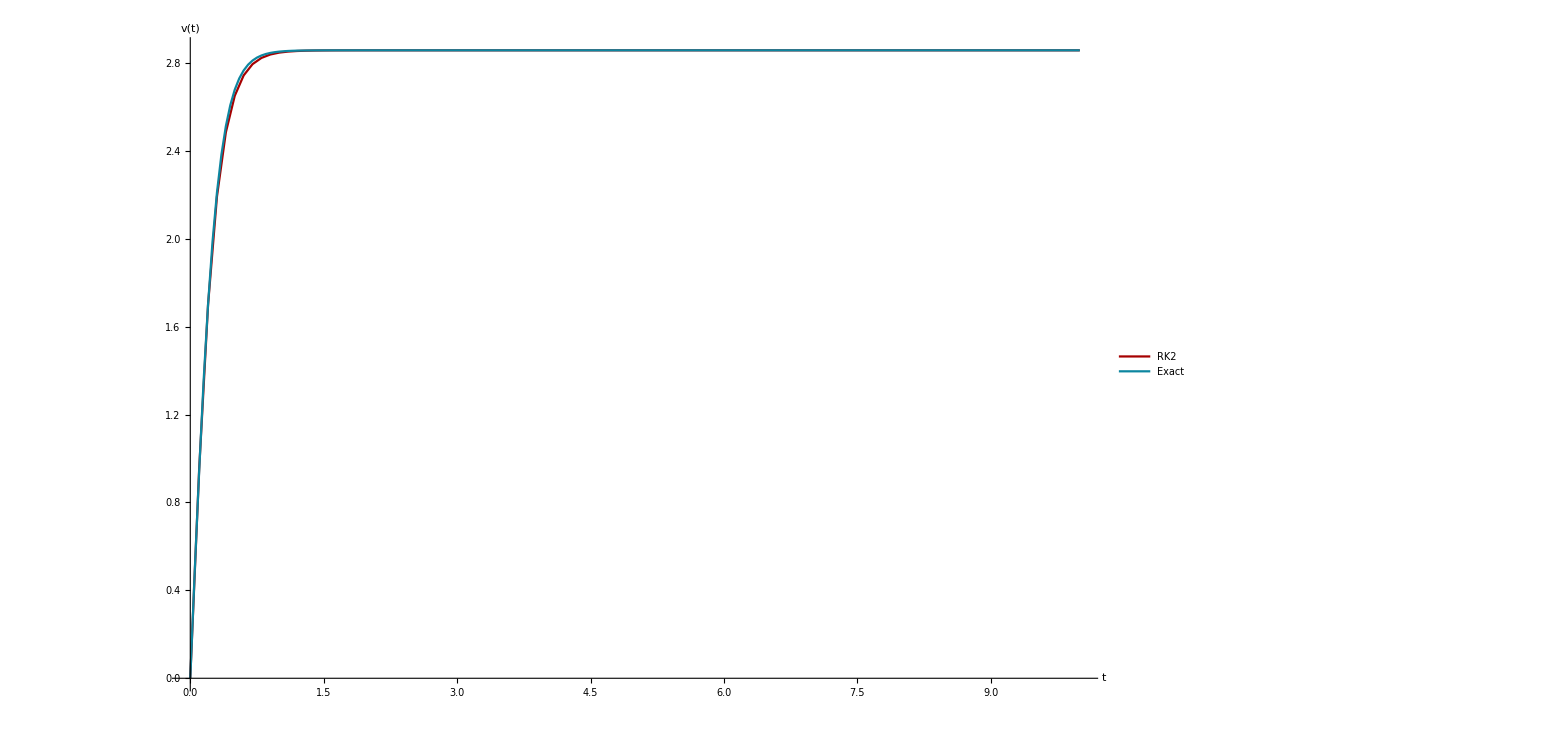

```mathematica
ListLinePlot[{solRK2,Table[{t,v[t]/. vexact[[1]]},{t,0,10,0.05}]},PlotLegends->{"RK2","Exact"},AxesLabel->{"t","v(t)"}]
```

Here, the RK2 slightly overshoots terminal velocity. Because, the nonlinear quadratic drag term introduces curvature that changes rapidly when velocity grows.

## 3. Runge-Kutta 4 (RK4 Method)

Runge-Kutta 4th Order (RK4) method:

k_1=f(t_n,y_n) ,   t_(n+1)=t_n+h ,
k_2=f(t_n+h/2,y_n+h/2 k_1)  ,
k_3=f(t_n+h/2,y_n+h/2 k_2)  ,
k_4=f(t_n+h,y_n+h k_3)  ,
y_(n+1)=y_n+h/6 (k_1+2 k_2+2 k_3+k_4) .

While the Euler method only uses the slope at the beginning of the interval, RK4 takes four different  samples of the slope (k_1 through k_4) across the interval h and calculates a weighted average.

```mathematica
RK4[f_,y0_,{t0_,tmax_},h_]:=
Module[{tlist,ylist,nsteps,k1,k2,k3,k4},
tlist=Range[t0,tmax,h];
nsteps=Length[tlist];
ylist=ConstantArray[0,nsteps];
ylist[[1]]=y0;

Do[
k1=f[tlist[[n]],ylist[[n]]];
k2=f[tlist[[n]]+h/2,ylist[[n]]+h/2 k1];
k3=f[tlist[[n]]+h/2,ylist[[n]]+h/2 k2];
k4=f[tlist[[n]]+h,ylist[[n]]+h k3];
ylist[[n+1]]=ylist[[n]]+(h/6) (k1+2 k2+2 k3+k4),
{n,1,nsteps-1}
];
Transpose[{tlist,ylist}]
]
```

Numerical Solutions

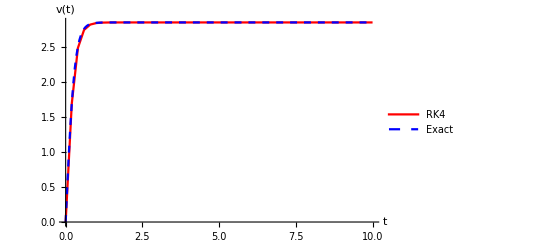

```mathematica
solRK4=RK4[f,0,{0,10},0.2];
ListLinePlot[{solRK4,Table[{t,v[t]/. vexact[[1]]},{t,0,10,0.05}]},PlotLegends->{"RK4","Exact"},PlotStyle->{{Red},{Blue,Dashed}},AxesLabel->{"t","v(t)"}]
```

Mean Global Error in RK4

```mathematica
tvals4=solRK4[[All,1]];
vRK4=solRK4[[All,2]];
vExact4=(v[#]/. vexact[[1]])&/@tvals4;
errorRK4=Abs[vRK4-vExact4];
MeanErrorRK4=Mean[errorRK4]
```

0.0009972

Mean Global Error in RK2

```mathematica
tvals2=solRK2[[All,1]];
vRK2=solRK2[[All,2]];
vExact2=(v[#]/. vexact[[1]])&/@tvals2;
errorRK2=Abs[vRK2-vExact2];
MeanErrorRK2=Mean[errorRK2]
```

0.0118445

Global error in RK4 ~ O(h^4) .

Problem-1:

Consider solving the initial value problem:   d/dt x= -2t x  ,  x(0)=1 using the RK2 and RK4 methods with step size h=0.2 . Find the approximate value of  x(1)?

```mathematica
f[t_,x_]:=-2 t x;
```

```mathematica
h=0.2;
```

```mathematica
solRK2=RK2[f,1,{0,1},h]
```

{{0.,1},{0.2,0.96},{0.4,0.849408},{0.6,0.693117},{0.8,0.522333},{1.,0.364379}}

The solution stored as {{t0, x0}, {t1, x1}, ..., {t5, x5}}

```mathematica
xAt1=solRK2[[-1,2]]
```

0.364379

```mathematica
solRK4=RK4[f,1,{0,1},h]
```

{{0.,1},{0.2,0.960789},{0.4,0.852143},{0.6,0.697676},{0.8,0.527298},{1.,0.367904}}

```mathematica
xAt1=solRK4[[-1,2]]
```

0.367904

Problem-2:

Let’s now a second-order ODE problem — the simple harmonic oscillator:

ẍ (t)=-x , x (0)=2 , ẋ (0)=0 .

Use the RK2 and RK4 methods with step size h=0.5. Find the approximate value of  x(5)and  v(5)?

Sol: Convert into first order equations  (matrix form)

d/dt(x
v)=(v
-x)   , where v=d/dt x .

let’s implement this in Mathematica.

```mathematica
f[t_,{x_,v_}]:={v,-x};
```

```mathematica
x0={2,0};
```

```mathematica
h=0.5;
solRK2=RK2[f,x0,{0,5},h]
```

{{0.,{2,0}},{0.5,{1.75,-1.}},{1.,{1.03125,-1.75}},{1.5,{0.0273438,-2.04688}},{2.,{-0.999512,-1.80469}},{2.5,{-1.77692,-1.07935}},{3.,{-2.09447,-0.0559692}},{3.5,{-1.86065,0.998264}},{4.,{-1.12894,1.80381}},{4.5,{-0.0859164,2.1428}},{5.,{0.996223,1.91791}}}

Solution structure: {{t0, {x0, v0}}, {t1, {x1, v1}}, ...}

```mathematica
xvSolAt5=solRK2[[-1,2]] (*return {x(5), v(5)}*)
```

{0.996223,1.91791}

```mathematica
xSol=Transpose[{solRK2[[All,1]],solRK2[[All,2,1]]}]
```

{{0.,2},{0.5,1.75},{1.,1.03125},{1.5,0.0273438},{2.,-0.999512},{2.5,-1.77692},{3.,-2.09447},{3.5,-1.86065},{4.,-1.12894},{4.5,-0.0859164},{5.,0.996223}}

```mathematica
xSolAt5=xSol[[-1,2]]
```

0.996223

```mathematica
vSol=Transpose[{solRK2[[All,1]],solRK2[[All,2,2]]}]
```

{{0.,0},{0.5,-1.},{1.,-1.75},{1.5,-2.04688},{2.,-1.80469},{2.5,-1.07935},{3.,-0.0559692},{3.5,0.998264},{4.,1.80381},{4.5,2.1428},{5.,1.91791}}

```mathematica
vSolAt5=vSol[[-1,2]]
```

1.91791

Damped Harmonic Oscillator

Let’s consider the equation

m d^2/dt^2 y(t) + γ d/dt y(t) + k x(t)=0

```mathematica
m=1;
γ=0.5;
k=4;
```

Ex.-4: Use RK4 and RK2 methods to solve the equation approximately.

LCR Circuit Analogy

L  d^2/dt^2 q(t) + R d/dt q(t) + 1/C_0 q(t)=0

Sol: Convert into first order equations  (matrix form)

d/dt(q
q̇)=(q̇
-R/L q̇-1/(L C_0)q)   , where  q̇=d/dt q .

```mathematica
Clear[L,R,C0]
```

```mathematica
L=1;
R=0.5;
C0=0.25;
```

```mathematica
q0={1,0};
```

```mathematica
f[t_,{q1_,q2_}]:={q2,-(R/L) q2-(1/(L C0)) q1};  (* q1=q, q2=q̇ *)
```

```mathematica
h=0.25;
solRK2=RK2[f,q0,{0,20},h];
```

```mathematica
qRK2=Transpose[{solRK2[[All,1]],solRK2[[All,2,1]]}]
```

{{0.,1},{0.25,0.875},{0.5,0.545898},{0.75,0.118889},{1.,-0.287803},{1.25,-0.574885},{1.5,-0.684603},{1.75,-0.610313},{2.,-0.39215},{2.25,-0.101516},{2.5,0.180438},{2.75,0.384242},{3.,0.468101},{3.25,0.425108},{3.5,0.280877},{3.75,0.0833279},{4.,-0.111903},{4.25,-0.256279},{4.5,-0.319666},{4.75,-0.295709},{5.,-0.200632},{5.25,-0.0665387},{5.5,0.0684751},{5.75,0.170548},{6.,0.218023},{6.25,0.205428},{6.5,0.142952},{6.75,0.0520598},{7.,-0.0411961},{7.25,-0.113225},{7.5,-0.148506},{7.75,-0.142526},{8.,-0.101616},{8.25,-0.0400957},{8.5,0.0242391},{8.75,0.0749749},{9.,0.101021},{9.25,0.0987601},{9.5,0.0720739},{9.75,0.0304965},{10.,-0.0138327},{10.25,-0.0495089},{10.5,-0.068627},{10.75,-0.068348},{11.,-0.0510147},{11.25,-0.022959},{11.5,0.00754875},{11.75,0.0325941},{12.,0.046556},{12.25,0.0472427},{12.5,0.0360383},{12.75,0.0171373},{13.,-0.00383308},{13.25,-0.0213877},{13.5,-0.0315382},{13.75,-0.0326147},{14.,-0.0254113},{14.25,-0.0126992},{14.5,0.00169791},{14.75,0.0139834},{15.,0.0213334},{15.25,0.0224887},{15.5,0.0178864},{15.75,0.00935185},{16.,-0.000520505},{16.25,-0.00910582},{16.5,-0.0144086},{16.75,-0.0154878},{17.,-0.0125686},{17.25,-0.00684932},{17.5,-0.0000879493},{17.75,0.00590306},{18.,0.00971623},{18.25,0.0106535},{18.5,0.00881754},{18.75,0.00499236},{19.,0.000367347},{19.25,-0.0038075},{19.5,-0.00654124},{19.75,-0.0073193},{20.,-0.00617636}}

```mathematica
ω0=Sqrt[1/(L C0)];
γ=R/(2 L);
ωd=Sqrt[ω0^2-γ^2];

qExact[t_]:=Exp[-γ t] Cos[ωd t]
```

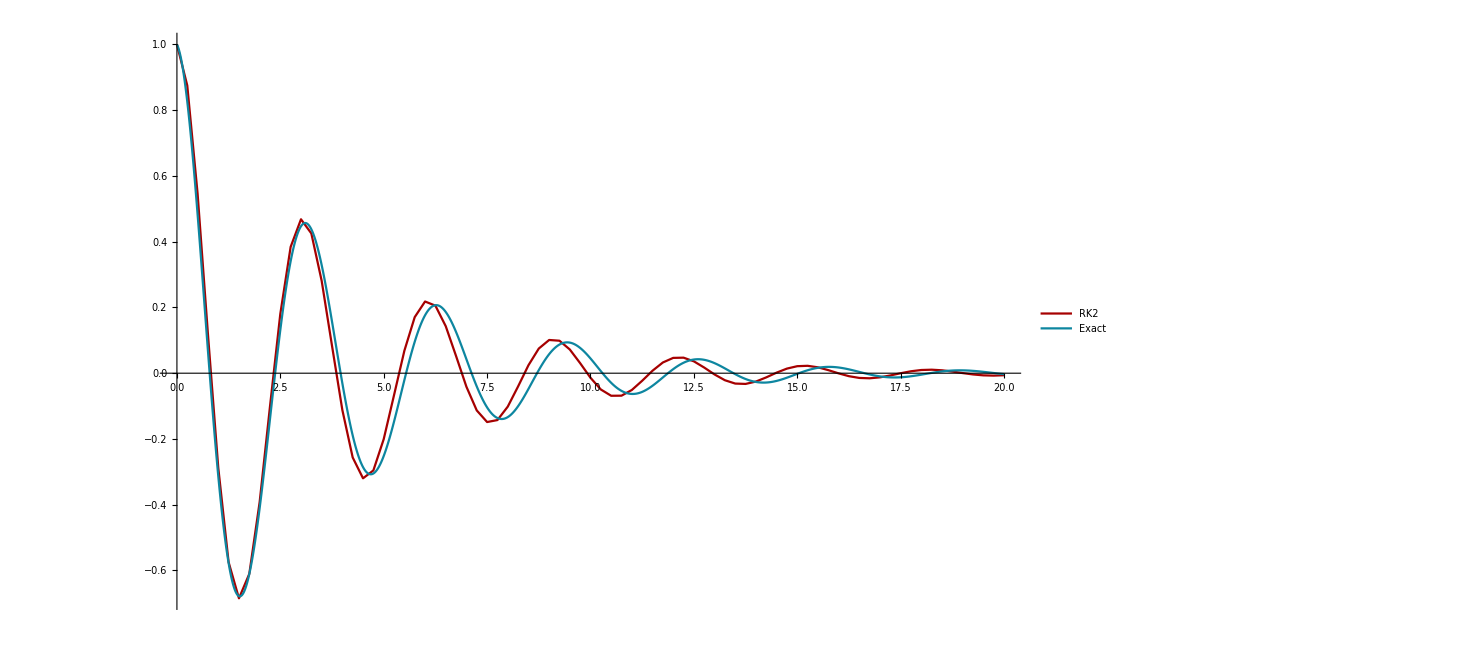

```mathematica
ListLinePlot[{qRK2,Table[{t,qExact[t]},{t,0,20,0.01}]},PlotLegends->{"RK2","Exact"},PlotRange->All]
```

```mathematica
h=0.25;
solRK4=RK4[f,q0,{0,20},h];
```

```mathematica
qRK4=Transpose[{solRK4[[All,1]],solRK4[[All,2,1]]}];
```

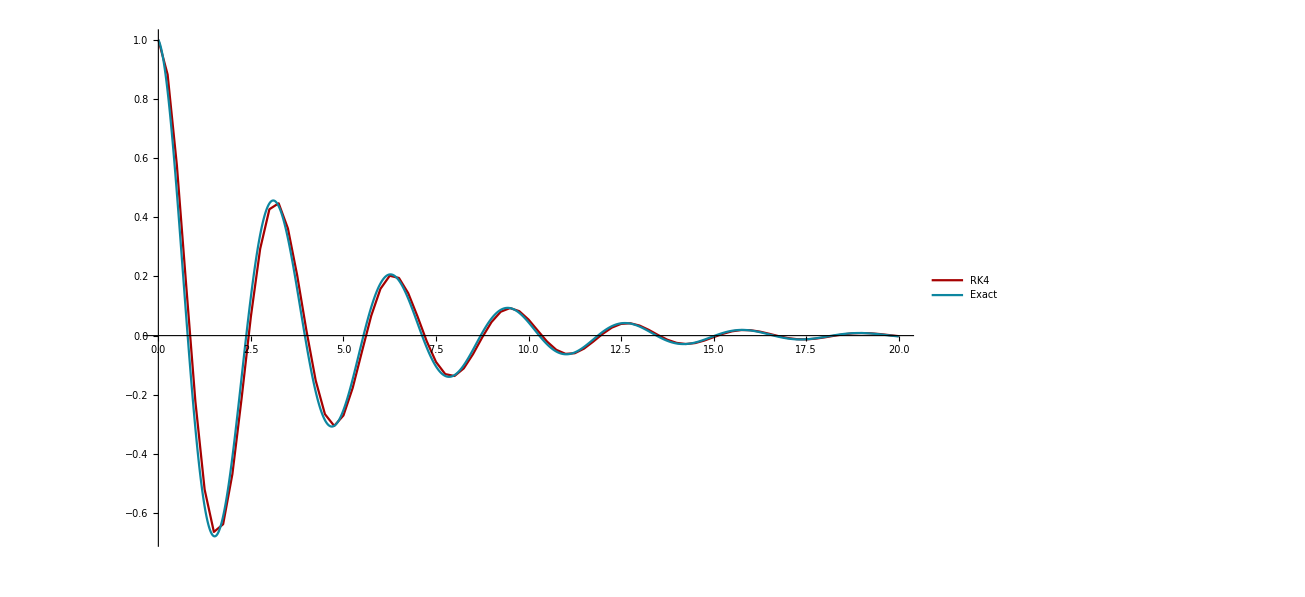

```mathematica
ListLinePlot[{qRK4,Table[{t,qExact[t]},{t,0,20,0.01}]},PlotLegends->{"RK4","Exact"},PlotRange->All]
```

```mathematica
solRK4[[All,2,1]]
```

{1,0.88265,0.576138,0.173146,-0.222344,-0.520282,-0.663619,-0.637549,-0.467954,-0.210679,0.0648311,0.29309,0.427164,0.447284,0.362203,0.203833,0.0171905,-0.151492,-0.265541,-0.305147,-0.269944}

```mathematica
errRK2=Mean[Abs[solRK2[[All,2,1]]-(qExact/@solRK2[[All,1]])]]
```

0.0308717

```mathematica
errRK4=Mean[Abs[solRK4[[All,2,1]]-(qExact/@solRK4[[All,1]])]]
```

0.0161847

Example: Van der Pol oscillator

Not all systems return to equilibrium. The nonlinear dynamics for the Van der Pol oscillator is described by

(d^2 x)/dt^2-μ(1-x^2)(d x)/dt+x=0

This can be written as a set of coupled equations:

(d v)/dt=μ(1-x^2) v -x ,
v=(d x)/dt,

```mathematica
mu = 1.0;
```

```mathematica
f[t_,{x_,v_}]:={v,mu (1-x^2) v-x};
```

```mathematica
x0={0.1,0};(*{x(0),v(0)}*)
```

```mathematica
h=0.1;
solRK2=RK2[f,x0,{0,50},h];
```

```mathematica
phaseData=solRK2[[All,2]];
```

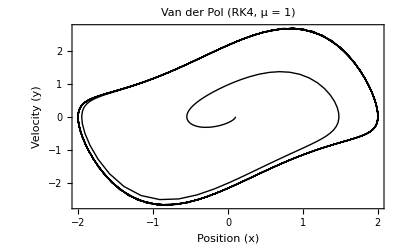

```mathematica
ListLinePlot[phaseData,PlotStyle->{Black,Thick},Frame->True,FrameLabel->{"Position (x)","Velocity (y)"},PlotLabel->"Van der Pol (RK4, μ = 1)"]
```

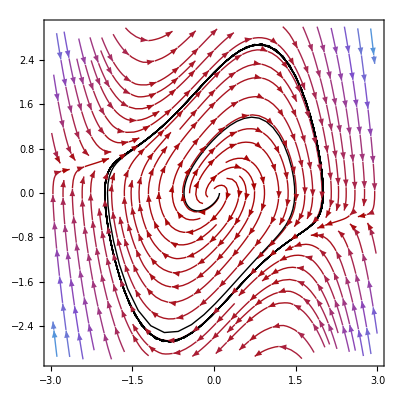

```mathematica
field=StreamPlot[{v,mu (1-x^2) v-x},{x,-3,3},{v,-3,3},StreamStyle->Arrowheads[0.02]];
Show[field,ListLinePlot[phaseData,PlotStyle->{Black,Thick}]]
```

Limit Cycle: A closed, isolated trajectory in phase space. It is a self-sustained periodic motion and it does NOT depend on initial conditions.

Solve using NDSolve:

```mathematica
vdp={x'[t]==v[t],v'[t]==mu (1-x[t]^2) v[t]-x[t]};
```

```mathematica
solutions=Table[NDSolveValue[{vdp,x[0]==ic[[1]],v[0]==ic[[2]]},{x[t],v[t]},{t,0,40}],{ic,{{0.1,0},{3,0},{-2,1}}}];
```

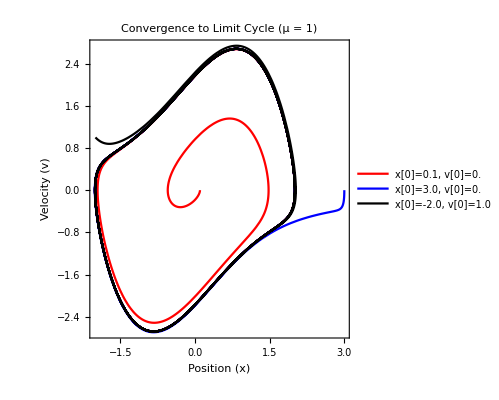

```mathematica
ParametricPlot[Evaluate[solutions],{t,0,40},PlotStyle->{Red,Blue,Black},Frame->True,FrameLabel->{"Position (x)","Velocity (v)"},PlotLabel->"Convergence to Limit Cycle (μ = 1)",PlotLegends->{"x[0]=0.1, v[0]=0.","x[0]=3.0, v[0]=0.","x[0]=-2.0, v[0]=1.0"}]
```

```mathematica
Manipulate[
Module[{vdp,solutions,field},
vdp={x'[t]==v[t],v'[t]==mu (1-x[t]^2) v[t]-x[t]};
solutions=Table[NDSolveValue[{vdp,x[0]==ic[[1]],v[0]==ic[[2]]},{x[t],v[t]},{t,0,50}],{ic,{{0.1,0.1},{2.5,2.5},{-2.5,-0.5}}}];
field=StreamPlot[{v,mu (1-x^2) v-x},{x,-3,3},{v,-3,3},StreamStyle->Arrowheads[0.02],StreamColorFunction->"Rainbow"];
Show[field,ParametricPlot[Evaluate[solutions],{t,0,50},PlotStyle->{Red,Blue,Black}],FrameLabel->{"Position (x)","Velocity (v)"},PlotLabel->Style["Phase Space & Limit Cycles",14]]],{{mu,1.0,"Nonlinearity (μ)"},0.1,4.0},SaveDefinitions->True]
```

If  μ=0 , its a pure harmonic oscillator (no limit cycle).